```mathematica
Quit[];
```

```mathematica
Import["/Users/conordyson/Documents/GitHub/BHPT/KerrGeodesics/KerrGeodesicsTest/Kernel/KerrGeoPlunge.m"]
```

```mathematica
SetDirectory@NotebookDirectory[];
PacletDirectoryLoad["."];
<<KerrGeodesics`
```

## ISSO Testing

### Testing ISSO Inclination

3.33239

{0.877583,2.7481}

<|Λ_(r_-)^-→-16.0705,Λ_(r_+)^-→-15.5594,Λ_(r_+)^+→-16.9537,Λ_(r_-)^+→-16.4426|>

{0.902968,1.30163,5.81623}

{10.,3.3,2.4,10.}

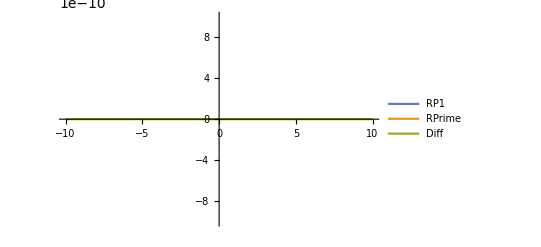

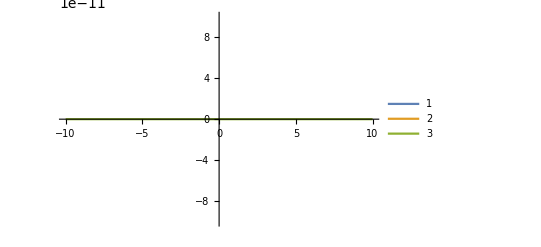

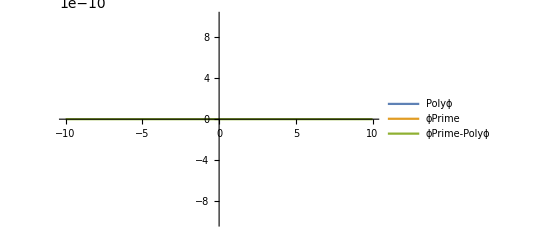

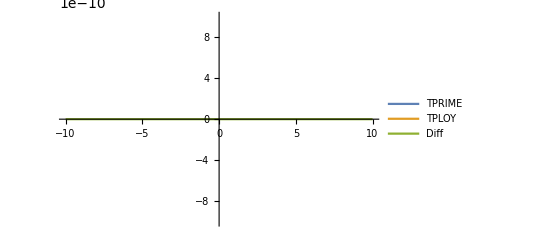

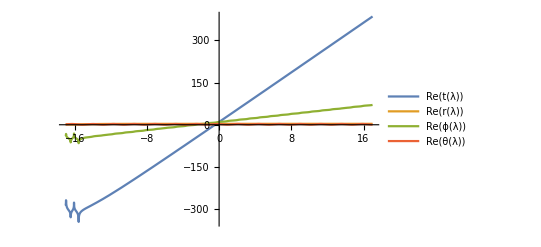

```mathematica
a =0.99;
M=1;
RP = 1+Sqrt[1-a^2];
RM = 1-Sqrt[1-a^2];
orbit = KerrGeoPlunge[a, "ISSOIncParam",0.5,{10,3.3,2.4,10}];
 orbit["RadialRoots"][[1]]
{Z1,Z2}=orbit["PolarRoots"]
{t,r,θ,ϕ} = orbit["Trajectory"];
orbit["HorizonCrossingTimeMino"]
{ϵ,L,Q} = {"ℰ","ℒ" ,"𝒬"}/.orbit["ConstantsOfMotion"]

z[λ_]:= Cos[θ[λ]];
{t[0],r[0],θ[0],ϕ[0]}

RPoly1[r_]:= (ϵ(r^2+a^2)-a*L)^2-(r^2-2M*r+a^2)(r^2+(a*ϵ-L)^2+Q);
Polyθ[λ_] := (z[λ]^2-Z1^2)*(a^2(1-ϵ^2)z[λ]^2-Z2^2)
Polyϕ[λ_]:= a/((r[λ]-RP)(r[λ]-RM))(ϵ(r[λ]^2+a^2)-a*L) + L/(1-z[λ]^2)-a*ϵ;
TPoly[λ_]:=  (r[λ]^2+a^2)/((r[λ]-RP)(r[λ]-RM))(ϵ(r[λ]^2+a^2)-a*L)-a^2 ϵ(1-z[λ]^2)+a*L;

Plot[{Re[RPoly1[r[λ]]], Re[(r'[λ])^2],Re[ (r'[λ])^2- RPoly1[r[λ]]]},{λ,-10,10}, PlotLegends->{RP1,RPrime,Diff},  PlotRange->{{-10,10},{-0.000000001,0.000000001}}]
Plot[{(z'[λ])^2, Polyθ[λ], (z'[λ])^2- Polyθ[λ]}, {λ,-10,10}, PlotLegends->Automatic ,PlotLegends->{PolyθQ,θQ,θQ-PolyθQ},  PlotRange->{{-10,10},{-0.0000000001,0.0000000001}}]
Plot[{Re[Polyϕ[λ]],Re[ϕ'[λ]],Re[ϕ'[λ]-Polyϕ[λ]]},{λ,-10,10},PlotLegends->{Polyϕ,ϕPrime,ϕPrime-Polyϕ},  PlotRange->{{-10,10},{-0.000000001,0.000000001}}]
Plot[{Re[t'[λ]],Re[ TPoly[λ] ], Re[t'[λ]- TPoly[λ]]},{λ,-10,10},PlotLegends->{TPRIME,TPLOY,Diff},  PlotRange->{{-10,10},{-0.000000001,0.000000001}}]
Plot[{Re[t[λ]],Re[ r[λ]],Re[ ϕ[λ]],Re[θ[λ]]},{λ,-17,17},PlotLegends->"Expressions", PlotRange->All]
```

KerrGeoPlungeFunction[…]

<|Λ_r_I^→±∞,Λ_r_Outer^→0.|>

<|Λ_(r_+)^+→-0.697145,Λ_(r_-)^+→-0.18608,Λ_(r_-)^-→0.18608,Λ_(r_+)^-→0.697145|>

{0.,0.83426,1.5708,0.}

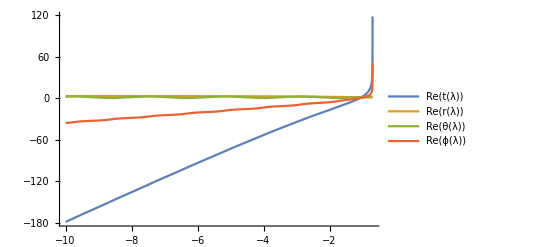

```mathematica
a =0.99;
M=1;
RP = 1+Sqrt[1-a^2];
RM = 1-Sqrt[1-a^2];
orbit = KerrGeoPlunge[a, "ISSOIncParam",0.5]
(*{10,3.3,2.4,10}*)
{t,r,θ,ϕ} = orbit["Trajectory"];
orbit["RadialRootCrossingTimeMino"]
orbit["HorizonCrossingTimeMino"]
{t[0],r[0],θ[0],ϕ[0]}
ee = 0.0001;
dd = 0.4036946674340016;
Plot[{Re[t[λ]],Re[r[λ]],Re[θ[λ]],Re[ϕ[λ]]},{λ,-10,-0.6971451631914674},PlotLegends->"Expressions", PlotRange->All]
```

### Testing ISSO Radial

8.8

{0.308479,4.19945}

<|Λ_(r_+)^+→-8.03589,Λ_(r_-)^+→-7.98793,Λ_(r_-)^-→-7.45272,Λ_(r_+)^-→-7.40476|>

{0.961423,-3.98624,1.67817}

{10.,8.7,1.7,10.}

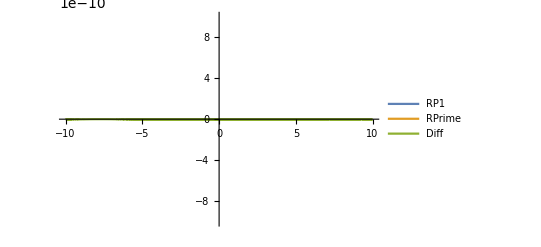

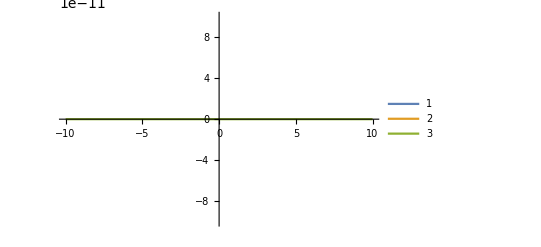

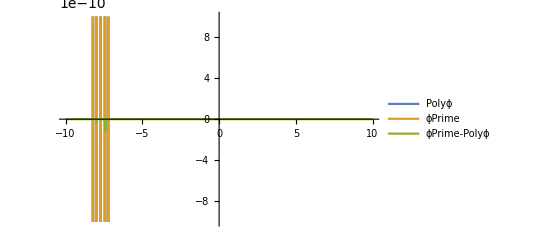

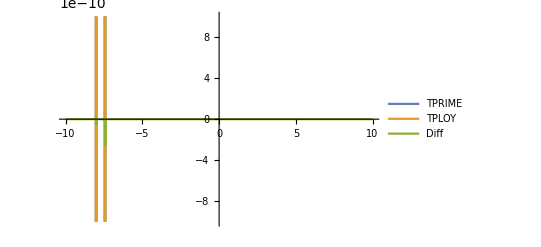

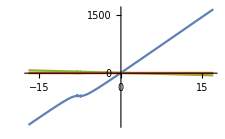

```mathematica
a =0.99;
M=1;
RP = 1+Sqrt[1-a^2];
RM = 1-Sqrt[1-a^2];
orbit = KerrGeoPlunge[a, "ISSORadialParam",8.8,{10,8.7,1.7,10}];
 orbit["RadialRoots"][[1]]
{Z1,Z2}=orbit["PolarRoots"]
{t,r,θ,ϕ} = orbit["Trajectory"];
orbit["HorizonCrossingTimeMino"]
{ϵ,L,Q} = {"ℰ","ℒ" ,"𝒬"}/.orbit["ConstantsOfMotion"]
z[λ_]:= Cos[θ[λ]];
{t[0],r[0],θ[0],ϕ[0]}

RPoly1[r_]:= (ϵ(r^2+a^2)-a*L)^2-(r^2-2M*r+a^2)(r^2+(a*ϵ-L)^2+Q);
Polyθ[λ_] := (z[λ]^2-Z1^2)*(a^2(1-ϵ^2)z[λ]^2-Z2^2)
Polyϕ[λ_]:= a/((r[λ]-RP)(r[λ]-RM))(ϵ(r[λ]^2+a^2)-a*L) + L/(1-z[λ]^2)-a*ϵ;
TPoly[λ_]:=  (r[λ]^2+a^2)/((r[λ]-RP)(r[λ]-RM))(ϵ(r[λ]^2+a^2)-a*L)-a^2 ϵ(1-z[λ]^2)+a*L;

Plot[{Re[RPoly1[r[λ]]], Re[(r'[λ])^2],Re[ (r'[λ])^2- RPoly1[r[λ]]]},{λ,-10,10}, PlotLegends->{RP1,RPrime,Diff},  PlotRange->{{-10,10},{-0.000000001,0.000000001}}]
Plot[{(z'[λ])^2, Polyθ[λ], (z'[λ])^2- Polyθ[λ]}, {λ,-10,10}, PlotLegends->Automatic ,PlotLegends->{PolyθQ,θQ,θQ-PolyθQ},  PlotRange->{{-10,10},{-0.0000000001,0.0000000001}}]
Plot[{Re[Polyϕ[λ]],Re[ϕ'[λ]],Re[ϕ'[λ]-Polyϕ[λ]]},{λ,-10,10},PlotLegends->{Polyϕ,ϕPrime,ϕPrime-Polyϕ},  PlotRange->{{-10,10},{-0.000000001,0.000000001}}]
Plot[{Re[t'[λ]],Re[ TPoly[λ] ], Re[t'[λ]- TPoly[λ]]},{λ,-10,10},PlotLegends->{TPRIME,TPLOY,Diff},  PlotRange->{{-10,10},{-0.000000001,0.000000001}}]
Plot[{Re[t[λ]],Re[ r[λ]],Re[ ϕ[λ]],Re[θ[λ]]},{λ,-17,17},PlotLegends->"Expressions", PlotRange->All]
```

## Generic Testing

### Real Root Test Parameters

{13.7746,5.83139,3.62996,0.00260618}

{0.708111,3.6115}

<|Λ_(r_+)^+→-0.703888,Λ_(r_-)^+→-0.0196025,Λ_(r_-)^-→0.0196025,Λ_(r_+)^-→0.703888|>

{0.956,2.55,6.54}

{0.,0.00260618,1.5708,0.}

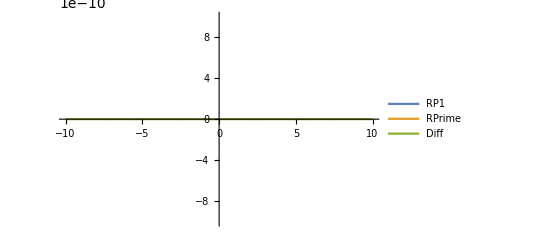

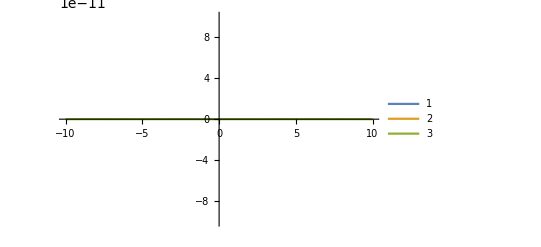

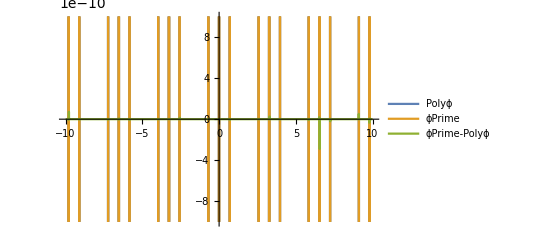

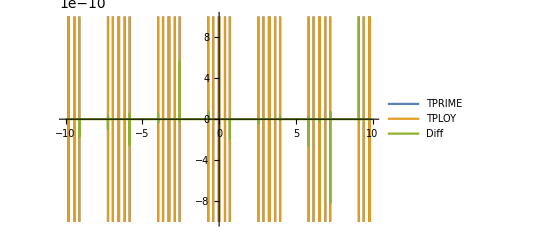

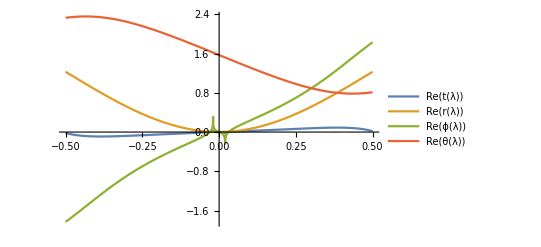

```mathematica
a =0.1;
ϵ = 0.956;
L =2.55;
Q =6.54;
M=1;
RP = 1+Sqrt[1-a^2];
RM = 1-Sqrt[1-a^2];
orbit = KerrGeoPlunge[a,{ϵ,L,Q}];
 orbit["RadialRoots"]
{Z1,Z2}=orbit["PolarRoots"]
{t,r,θ,ϕ} = orbit["Trajectory"];
orbit["HorizonCrossingTimeMino"]
{ϵ,L,Q} = {"ℰ","ℒ" ,"𝒬"}/.orbit["ConstantsOfMotion"]
z[λ_]:= Cos[θ[λ]];
{t[0],r[0],θ[0],ϕ[0]}

RPoly1[r_]:= (ϵ(r^2+a^2)-a*L)^2-(r^2-2M*r+a^2)(r^2+(a*ϵ-L)^2+Q)
Polyθ[λ_] := (z[λ]^2-Z1^2)*(a^2(1-ϵ^2)z[λ]^2-Z2^2)
Polyϕ[λ_]:= a/((r[λ]-RP)(r[λ]-RM))(ϵ(r[λ]^2+a^2)-a*L) + L/(1-z[λ]^2)-a*ϵ;
TPoly[λ_]:=  (r[λ]^2+a^2)/((r[λ]-RP)(r[λ]-RM))(ϵ(r[λ]^2+a^2)-a*L)-a^2 ϵ(1-z[λ]^2)+a*L;

Plot[{Re[RPoly1[r[λ]]], Re[(r'[λ])^2],Re[ (r'[λ])^2- RPoly1[r[λ]]]},{λ,-10,10}, PlotLegends->{RP1,RPrime,Diff},  PlotRange->{{-10,10},{-0.000000001,0.000000001}}]
Plot[{(z'[λ])^2, Polyθ[λ], (z'[λ])^2- Polyθ[λ]}, {λ,-10,10}, PlotLegends->Automatic ,PlotLegends->{PolyθQ,θQ,θQ-PolyθQ},  PlotRange->{{-10,10},{-0.0000000001,0.0000000001}}]
Plot[{Re[Polyϕ[λ]],Re[ϕ'[λ]],Re[ϕ'[λ]-Polyϕ[λ]]},{λ,-10,10},PlotLegends->{Polyϕ,ϕPrime,ϕPrime-Polyϕ},  PlotRange->{{-10,10},{-0.000000001,0.000000001}}]
Plot[{Re[t'[λ]],Re[ TPoly[λ] ], Re[t'[λ]- TPoly[λ]]},{λ,-10,10},PlotLegends->{TPRIME,TPLOY,Diff},  PlotRange->{{-10,10},{-0.000000001,0.000000001}}]
Plot[{Re[t[λ]],Re[ r[λ]],Re[ ϕ[λ]],Re[θ[λ]]},{λ,-0.5,0.5},PlotLegends->"Expressions", PlotRange->All]
```

```mathematica
path[λ_]:= {Re[r[λ]]*Sin[Re[ϕ[λ]]]*Sin[Re[θ[λ]]],Re[r[λ]]*Sin[Re[θ[λ]]]*Cos[Re[ϕ[λ]]],Re[r[λ]]*Cos[Re[θ[λ]]]}

P1 = ParametricPlot3D[path[λ],{λ,-10,10},ImageSize->400,MaxRecursion->14, PlotStyle->Red,PlotRange->All];
P2 =ParametricPlot3D[{RP*Sin[u] Sin[v],RP*Cos[u] Sin[v],RP*Cos[v]},{u,-π,π},{v,-π,π},ImageSize->300,MaxRecursion->10,PlotStyle->{Opacity[1],Black,Specularity[White,10]}, Lighting->"Neutral",Axes->None,Mesh->None,PlotRange->All];
Show[P1,P2]
```

-Graphics3D-

```mathematica
(* Gives non divergence at the horizon for azimuthal component a =0.1;
ϵ = 0.956;
L =2.55;
Q =26.54;
M=1;*)
```

### Complex Root Test Parameters

2.68191

{0.00402417,1.99585,0.0000611378-5.74841 ⅈ,0.0000611378+5.74841 ⅈ}

{0.896192,5.74843}

<|Λ_(r_+)^+→-0.528043,Λ_(r_-)^+→-0.00775097,Λ_(r_-)^-→0.00775097,Λ_(r_+)^-→0.528043|>

{0.00056,2.55,26.54}

{0.,0.00402417,1.5708,0.}

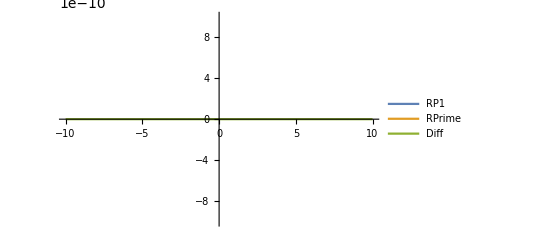

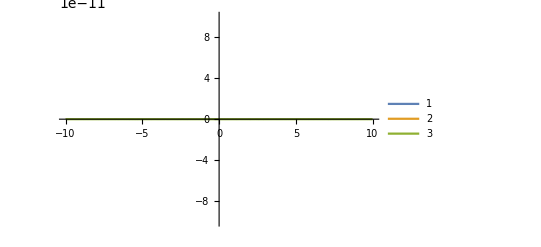

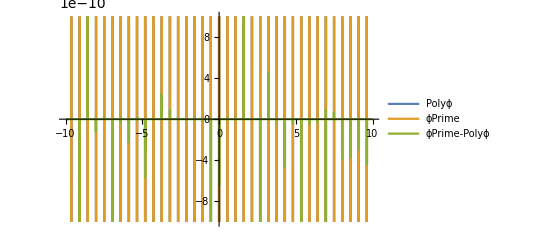

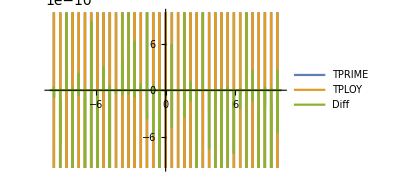

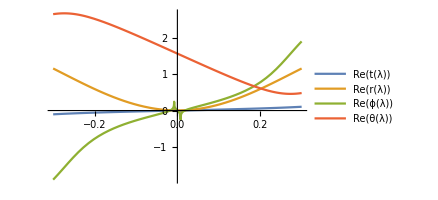

```mathematica
a =0.1;
ϵ = 0.00056;
L =2.55;
Q =26.54;
M=1;
RP = 1+Sqrt[1-a^2];
RM = 1-Sqrt[1-a^2];
orbit = KerrGeoPlunge[a,{ϵ,L,Q}];
 orbit["RadialRoots"]
{Z1,Z2}=orbit["PolarRoots"]
{t,r,θ,ϕ} = orbit["Trajectory"];
orbit["HorizonCrossingTimeMino"]
{ϵ,L,Q} = {"ℰ","ℒ" ,"𝒬"}/.orbit["ConstantsOfMotion"]
z[λ_]:= Cos[θ[λ]];
{t[0],r[0],θ[0],ϕ[0]}

RPoly1[r_]:= (ϵ(r^2+a^2)-a*L)^2-(r^2-2M*r+a^2)(r^2+(a*ϵ-L)^2+Q)
Polyθ[λ_] := (z[λ]^2-Z1^2)*(a^2(1-ϵ^2)z[λ]^2-Z2^2)
Polyϕ[λ_]:= a/((r[λ]-RP)(r[λ]-RM))(ϵ(r[λ]^2+a^2)-a*L) + L/(1-z[λ]^2)-a*ϵ;
TPoly[λ_]:=  (r[λ]^2+a^2)/((r[λ]-RP)(r[λ]-RM))(ϵ(r[λ]^2+a^2)-a*L)-a^2 ϵ(1-z[λ]^2)+a*L;

Plot[{Re[RPoly1[r[λ]]], Re[(r'[λ])^2],Re[ (r'[λ])^2- RPoly1[r[λ]]]},{λ,-10,10}, PlotLegends->{RP1,RPrime,Diff},  PlotRange->{{-10,10},{-0.000000001,0.000000001}}]
Plot[{(z'[λ])^2, Polyθ[λ], (z'[λ])^2- Polyθ[λ]}, {λ,-10,10}, PlotLegends->Automatic ,PlotLegends->{PolyθQ,θQ,θQ-PolyθQ},  PlotRange->{{-10,10},{-0.0000000001,0.0000000001}}]
Plot[{Re[Polyϕ[λ]],Re[ϕ'[λ]],Re[ϕ'[λ]-Polyϕ[λ]]},{λ,-10,10},PlotLegends->{Polyϕ,ϕPrime,ϕPrime-Polyϕ},  PlotRange->{{-10,10},{-0.000000001,0.000000001}}]
Plot[{Re[t'[λ]],Re[ TPoly[λ] ], Re[t'[λ]- TPoly[λ]]},{λ,-10,10},PlotLegends->{TPRIME,TPLOY,Diff},  PlotRange->{{-10,10},{-0.000000001,0.000000001}}]
Plot[{Re[t[λ]],Re[ r[λ]],Re[ ϕ[λ]],Re[θ[λ]]},{λ,-0.3,0.3},PlotLegends->"Expressions", PlotRange->All]
```

### Real Root Test Parameters ; 3 roots inside inner Horizon

```mathematica
a =0.1;
ϵ = 0.956;
L =2.55;
Manipulate[Manipulate[Manipulate[Manipulate[Plot[(ϵ(r^2+a^2)-a*L)^2-(r^2-2M*r+a^2)(r^2+(a*ϵ-L)^2+Q),{r,0,1}, PlotLabel->{a,ϵ,L,Q }],{Q,0,12}],{L,0,10}], {ϵ,0,1}], {a,0,1}]
```

```mathematica
a
ϵ
L
Q
```

```mathematica
0.1
0.956
2.55
26.54
```

1.16072

{0.24678,5.77925×10^-8,1.19761,0.576223}

<|Λ_(r_+)^+→-4.15405,Λ_(r_-)^+→-2.73658,Λ_(r_-)^-→2.73658,Λ_(r_+)^-→4.15405|>

{0.101,0.39,1.×10^-8}

{0.,0.576223,1.5708,0.}

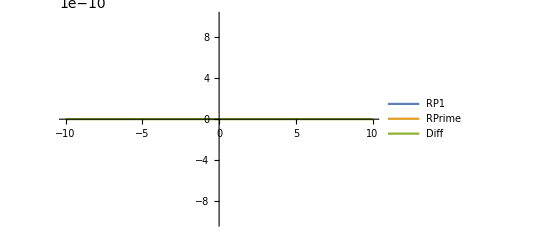

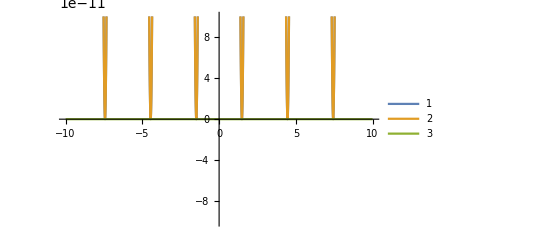

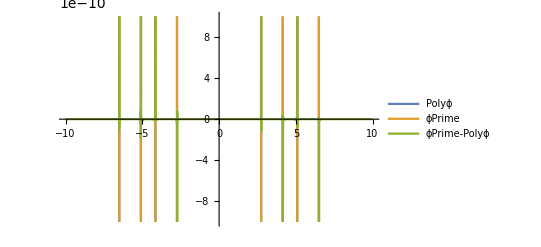

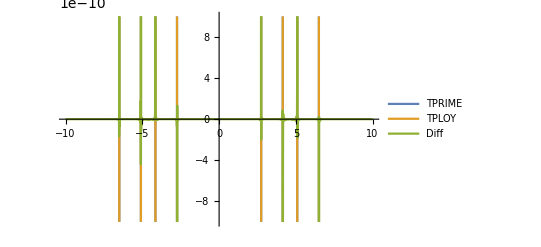

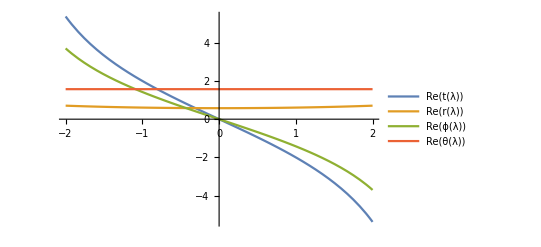

```mathematica
a = 0.987;
ϵ = 0.101;
L = 0.39;
Q = 0.00000001;
M=1;
RP = 1+Sqrt[1-a^2]
RM = 1-Sqrt[1-a^2];
orbit = KerrGeoPlunge[a,{ϵ,L,Q}];
 orbit["RadialRoots"]
{Z1,Z2}=orbit["PolarRoots"];
{t,r,θ,ϕ} = orbit["Trajectory"];
orbit["HorizonCrossingTimeMino"]
{ϵ,L,Q} = {"ℰ","ℒ" ,"𝒬"}/.orbit["ConstantsOfMotion"]
z[λ_]:= Cos[θ[λ]];
{t[0],r[0],θ[0],ϕ[0]}

RPoly1[r_]:= (ϵ(r^2+a^2)-a*L)^2-(r^2-2M*r+a^2)(r^2+(a*ϵ-L)^2+Q)
Polyθ[λ_] := (z[λ]^2-Z1^2)*(a^2(1-ϵ^2)z[λ]^2-Z2^2)
Polyϕ[λ_]:= a/((r[λ]-RP)(r[λ]-RM))(ϵ(r[λ]^2+a^2)-a*L) + L/(1-z[λ]^2)-a*ϵ;
TPoly[λ_]:=  (r[λ]^2+a^2)/((r[λ]-RP)(r[λ]-RM))(ϵ(r[λ]^2+a^2)-a*L)-a^2 ϵ(1-z[λ]^2)+a*L;

Plot[{Re[RPoly1[r[λ]]], Re[(r'[λ])^2],Re[ (r'[λ])^2- RPoly1[r[λ]]]},{λ,-10,10}, PlotLegends->{RP1,RPrime,Diff},  PlotRange->{{-10,10},{-0.000000001,0.000000001}}]
Plot[{(z'[λ])^2, Polyθ[λ], (z'[λ])^2- Polyθ[λ]}, {λ,-10,10}, PlotLegends->Automatic ,PlotLegends->{PolyθQ,θQ,θQ-PolyθQ},  PlotRange->{{-10,10},{-0.0000000001,0.0000000001}}]
Plot[{Re[Polyϕ[λ]],Re[ϕ'[λ]],Re[ϕ'[λ]-Polyϕ[λ]]},{λ,-10,10},PlotLegends->{Polyϕ,ϕPrime,ϕPrime-Polyϕ},  PlotRange->{{-10,10},{-0.000000001,0.000000001}}]
Plot[{Re[t'[λ]],Re[ TPoly[λ] ], Re[t'[λ]- TPoly[λ]]},{λ,-10,10},PlotLegends->{TPRIME,TPLOY,Diff},  PlotRange->{{-10,10},{-0.000000001,0.000000001}}]
Plot[{Re[t[λ]],Re[ r[λ]],Re[ ϕ[λ]],Re[θ[λ]]},{λ,-2,2},PlotLegends->"Expressions", PlotRange->All]
```

```mathematica
1.1607202538574404
```

1.16072

```mathematica
path[λ_]:= {Re[r[λ]]*Sin[Re[ϕ[λ]]]*Sin[Re[θ[λ]]],Re[r[λ]]*Sin[Re[θ[λ]]]*Cos[Re[ϕ[λ]]],Re[r[λ]]*Cos[Re[θ[λ]]]}

P1 = ParametricPlot3D[path[λ],{λ,0,10},ImageSize->400,MaxRecursion->14, PlotStyle->Red,PlotRange->All];
P2 =ParametricPlot3D[{RP*Sin[u] Sin[v],RP*Cos[u] Sin[v],RP*Cos[v]},{u,-π,π},{v,-π,π},ImageSize->300,MaxRecursion->10,PlotStyle->{Opacity[0],Black,Specularity[White,10]}, Lighting->"Neutral",Axes->None,Mesh->None,PlotRange->All];
Show[P1,P2]
```

-Graphics3D-

```mathematica
(* Gives non divergence at the horizon for azimuthal component a =0.1;
ϵ = 0.956;
L =2.55;
Q =26.54;
M=1;*)
```

```mathematica
orbit["RadialRoots"]
RP
```

{0.24678,5.77925×10^-8,1.19761,0.576223}

1.16072